# 탐색적 방법으로 풀어보는 수학 문제

전경원

```mathematica
DateString[]
```

Fri 17 Dec 2021 12:14:51

## 문제 1

-Graphics-

### 풀이

g(x)를 구해봅시다.

```mathematica
g[x]==3f[x]+4Cos[f[x]]
%/.f[x]->6π(x-1)^2
```

g[x]==4 Cos[f[x]]+3 f[x]

g[x]==18 π (-1+x)^2+4 Cos[6 π (-1+x)^2]

주어진 구간에 대해서 g(x)의 그래프를 그려보면 극소점의 개수를 파악할 수 있겠군요.

18 π (-1+x)^2+4 Cos[6 π (-1+x)^2]

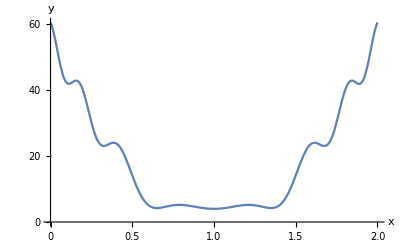

```mathematica
18 π (-1+x)^2+4 Cos[6 π (-1+x)^2]
Plot[%,{x,0,2},AxesLabel->{x,y}]
```

극소점의 개수는 대략 7개로 보입니다. 극값을 구해서 맞는지 확인해보지요.

```mathematica
D[g[x],x]==0
%/.g->Function[x,18 π (-1+x)^2+4 Cos[6 π (-1+x)^2]]
Reduce[%,x]//FullSimplify[#,C[1]∈Integers]&//Solve[#,x]&//Flatten//Thread[#,Rule]&//Last
```

g'[x]==0

36 π (-1+x)-48 π (-1+x) Sin[6 π (-1+x)^2]==0

{1,(6 √π-√6 √(π-ArcSin[3/4]+2 π C[1]))/(6 √π),(6 √π+√6 √(π-ArcSin[3/4]+2 π C[1]))/(6 √π),(6 √π-√6 √(ArcSin[3/4]+2 π C[1]))/(6 √π),(6 √π+√6 √(ArcSin[3/4]+2 π C[1]))/(6 √π)}

극값의 개수를 세어볼까요?

```mathematica
{1,(6 √π-√6 √(π-ArcSin[3/4]+2 π C[1]))/(6 √π),(6 √π+√6 √(π-ArcSin[3/4]+2 π C[1]))/(6 √π),(6 √π-√6 √(ArcSin[3/4]+2 π C[1]))/(6 √π),(6 √π+√6 √(ArcSin[3/4]+2 π C[1]))/(6 √π)}/.C[1]->C
Table[%,{C,0,5}]//Flatten//Union
Select[%,0<#<2&]//Length
```

{1,(6 √π-√6 √(π+2 C π-ArcSin[3/4]))/(6 √π),(6 √π+√6 √(π+2 C π-ArcSin[3/4]))/(6 √π),(6 √π-√6 √(2 C π+ArcSin[3/4]))/(6 √π),(6 √π+√6 √(2 C π+ArcSin[3/4]))/(6 √π)}

{1,(6 √π-√(6 (π-ArcSin[3/4])))/(6 √π),(6 √π+√(6 (π-ArcSin[3/4])))/(6 √π),(6 √π-√(6 (3 π-ArcSin[3/4])))/(6 √π),(6 √π+√(6 (3 π-ArcSin[3/4])))/(6 √π),(6 √π-√(6 (5 π-ArcSin[3/4])))/(6 √π),(6 √π+√(6 (5 π-ArcSin[3/4])))/(6 √π),(6 √π-√(6 (7 π-ArcSin[3/4])))/(6 √π),(6 √π+√(6 (7 π-ArcSin[3/4])))/(6 √π),(6 √π-√(6 (9 π-ArcSin[3/4])))/(6 √π),(6 √π+√(6 (9 π-ArcSin[3/4])))/(6 √π),(6 √π-√(6 (11 π-ArcSin[3/4])))/(6 √π),(6 √π+√(6 (11 π-ArcSin[3/4])))/(6 √π),(6 √π-√(6 ArcSin[3/4]))/(6 √π),(6 √π+√(6 ArcSin[3/4]))/(6 √π),(6 √π-√(6 (2 π+ArcSin[3/4])))/(6 √π),(6 √π+√(6 (2 π+ArcSin[3/4])))/(6 √π),(6 √π-√(6 (4 π+ArcSin[3/4])))/(6 √π),(6 √π+√(6 (4 π+ArcSin[3/4])))/(6 √π),(6 √π-√(6 (6 π+ArcSin[3/4])))/(6 √π),(6 √π+√(6 (6 π+ArcSin[3/4])))/(6 √π),(6 √π-√(6 (8 π+ArcSin[3/4])))/(6 √π),(6 √π+√(6 (8 π+ArcSin[3/4])))/(6 √π),(6 √π-√(6 (10 π+ArcSin[3/4])))/(6 √π),(6 √π+√(6 (10 π+ArcSin[3/4])))/(6 √π)}

13

x = 1 에 있는 극소값을 중심으로 양쪽으로 6개씩 극값이 있습니다. 이중 극대와 극소가 짝을 이루므로, 양쪽으로 3개씩 극소가 있으므로 극소가 되는 x의 개수는 모두 7개 입니다.

## 문제 2

-Graphics-

### 풀이

부분적분을 적용하면,

```mathematica
∫_1^8 x f'[x]ⅆx==(x f[x]/.x->8)-(x f[x]/.x->1)-∫_1^8 f[x]ⅆx
```

∫_1^8 x f'[x]ⅆx==-f[1]+8 f[8]-∫_1^8 f[x]ⅆx

문제에서 주어진 f(x)와 g(x)의 관계를 이용해서,

```mathematica
g[2x]==2f[x]/.x->1/.f[1]->1
f/@%/.f[g[x_]]->x
```

g[2]==2

2==f[2]

```mathematica
g[2x]==2f[x]/.x->2/.f[2]->2
f/@%/.f[g[x_]]->x
```

g[4]==4

4==f[4]

```mathematica
g[2x]==2f[x]/.x->4/.f[4]->4
f/@%/.f[g[x_]]->x
```

g[8]==8

8==f[8]

따라서

```mathematica
∫_1^8 x f'[x]ⅆx==-f[1]+8 f[8]-∫_1^8 f[x]ⅆx
%/.{f[1]->1,f[8]->8}/.∫_1^8 f[x]ⅆx->∫_1^2 f[x]ⅆx+∫_2^4 f[x]ⅆx+∫_4^8 f[x]ⅆx
```

∫_1^8 x f'[x]ⅆx==-f[1]+8 f[8]-∫_1^8 f[x]ⅆx

∫_1^8 x f'[x]ⅆx==63-∫_1^2 f[x]ⅆx-∫_2^4 f[x]ⅆx-∫_4^8 f[x]ⅆx

구간 x=[2,4]과 x=[4,8]에서 f(x)와 g(x)의 적분값은 아래 그래프에서 색칠한 부분에 해당한다.

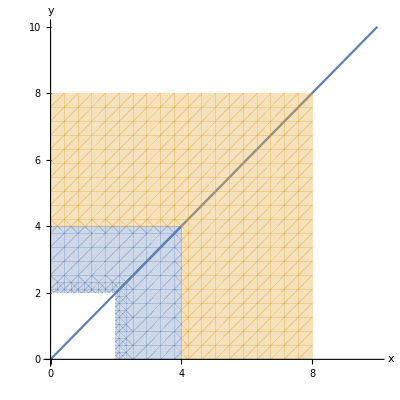

```mathematica
Show[{Plot[x,{x,0,10}],Plot[x,{x,2,4},PlotRange->{0,8}],RegionPlot[{2<=y<=4&&y>=x||2<=x<=4&&y<=x,4<=y<=8&&y>=x||4<=x<=8&&y<=x},{x,0,8},{y,0,8},BoundaryStyle->None]},AxesLabel->{x,y},AspectRatio->1]
```

구간 x=[2,4]에서 색칠한 부분의 넓이는

```mathematica
S==2((2+4)2)/2
```

S==12

이므로, S에서 g(x)의 적분값을 빼면 f(x)의 적분값을 얻을 수 있다. 이때 구간 x=[2,4]에서 g(x)의 적분 값은

```mathematica
∫_2^4 g[x]ⅆx->∫_1^2 g[2y]2ⅆy(*x/2==y*)
%/.y->x/.g[2 x]->2f[x]/.∫_1^2 4 f[x]ⅆx->4∫_1^2 f[x]ⅆx
%/.∫_1^2 f[x]ⅆx->5/4
```

∫_2^4 g[x]ⅆx→∫_1^2 2 g[2 y]ⅆy

∫_2^4 g[x]ⅆx→4 ∫_1^2 f[x]ⅆx

∫_2^4 g[x]ⅆx→5

이므로, 이로부터 f(x)의 적분값을 구할 수 있다.

```mathematica
∫_2^4 f[x]ⅆx->S-∫_2^4 g[x]ⅆx
%/.{S->12,∫_2^4 g[x]ⅆx->5}
```

∫_2^4 f[x]ⅆx→S-∫_2^4 g[x]ⅆx

∫_2^4 f[x]ⅆx→7

g(x)를 구간 x=[4,8]에 대해서 적분하면,

```mathematica
∫_4^8 g[x]ⅆx->∫_2^4 g[2y]2ⅆy(*x/2==y*)
%/.y->x/.g[2 x]->2f[x]/.∫_a_^b_ 4 f[x]ⅆx->4∫_a^b f[x]ⅆx
%/.∫_2^4 f[x]ⅆx->7
```

∫_4^8 g[x]ⅆx→∫_2^4 2 g[2 y]ⅆy

∫_4^8 g[x]ⅆx→4 ∫_2^4 f[x]ⅆx

∫_4^8 g[x]ⅆx→28

구간 x=[2,4]에서 색칠한 부분의 넓이는

```mathematica
S==2((4+8)4)/2
```

S==48

```mathematica
∫_4^8 f[x]ⅆx->S-∫_4^8 g[x]ⅆx
%/.{S->48,∫_4^8 g[x]ⅆx->28}
```

∫_4^8 f[x]ⅆx→S-∫_4^8 g[x]ⅆx

∫_4^8 f[x]ⅆx→20

이를 종합하면,

```mathematica
∫_1^8 x f'[x]ⅆx==63-∫_1^2 f[x]ⅆx-∫_2^4 f[x]ⅆx-∫_4^8 f[x]ⅆx
%/.{∫_1^2 f[x]ⅆx->5/4,∫_2^4 f[x]ⅆx->7,∫_4^8 f[x]ⅆx->20}
```

∫_1^8 x f'[x]ⅆx==63-∫_1^2 f[x]ⅆx-∫_2^4 f[x]ⅆx-∫_4^8 f[x]ⅆx

∫_1^8 x f'[x]ⅆx==139/4

결과의 분자와 분모를 더하면,

```mathematica
p+q==139+4
```

p+q==143

## 문제 3

-Graphics-

### 풀이

전제 조건에 해당하는 a_5+b_5>=7을 만족하는 경우의 수는

```mathematica
Tuples[Range[6],5];
Map[Which[#>=5,{W,W},#<=4,{B}]&,%,{2}];
Select[%,Length@Flatten@#>=7&]
%//Length
```

{{{B},{B},{B},{W,W},{W,W}},{{B},{B},{B},{W,W},{W,W}},{{B},{B},{B},{W,W},{W,W}},{{B},{B},{B},{W,W},{W,W}},{{B},{B},{B},{W,W},{W,W}},4183,{{W,W},{W,W},{W,W},{W,W},{B}},{{W,W},{W,W},{W,W},{W,W},{B}},{{W,W},{W,W},{W,W},{W,W},{W,W}},{{W,W},{W,W},{W,W},{W,W},{W,W}}}
 |  |  |  |

4192

a_k=b_k 가 되려면 4 이하가 반드시 두 번은 나와야 하며 첫 세번의 시행에서 4이하가 두 번, 5 이상이 한 번은 반드시 나와야 한다. 이러한 경우의 수는

```mathematica
Tuples[Range[6],5];
Map[Which[#>=5,{W,W},#<=4,{B}]&,%,{2}];
Select[%,Length@Flatten@#>=7&];
Select[%,Count[#[[1;;3]],{B}]>=2&];
Select[%,Count[#[[1;;3]],{W,W}]>=1&]
%//Length
```

{{{B},{B},{W,W},{B},{W,W}},{{B},{B},{W,W},{B},{W,W}},{{B},{B},{W,W},{B},{W,W}},{{B},{B},{W,W},{B},{W,W}},{{B},{B},{W,W},{B},{W,W}},1911,{{W,W},{B},{B},{W,W},{B}},{{W,W},{B},{B},{W,W},{B}},{{W,W},{B},{B},{W,W},{W,W}},{{W,W},{B},{B},{W,W},{W,W}}}
 |  |  |  |

1920

따라서, 확률  q/p는

```mathematica
q/p==1920/4192
Numerator@#+Denominator@#&/@%
```

q/p==60/131

p+q==191

## -Graphics-

함수 f(x)의 그래프를 구간 [0, π/4]에서 그려보죠.

f[x]==(Piecewise[{{Cos[x], Cos[x]≥Sin[x]}, {Sin[x], Cos[x]<Sin[x]}, {0, True}}])

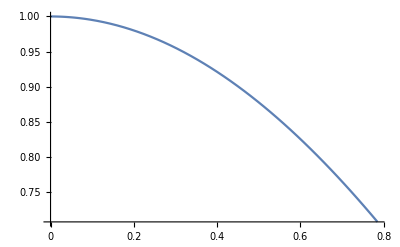

```mathematica
f[x]==Piecewise[{{Cos[x], Cos[x]>=Sin[x]}, {Sin[x], Cos[x]<Sin[x]}}]
Plot[%[[2]],{x,0,π/4}]
```

사실, 이 구간에서 f(x)는 cos(x)와 같습니다.

f[x]==(Piecewise[{{Cos[x], Cos[x]≥Sin[x]}, {Sin[x], Cos[x]<Sin[x]}, {0, True}}])

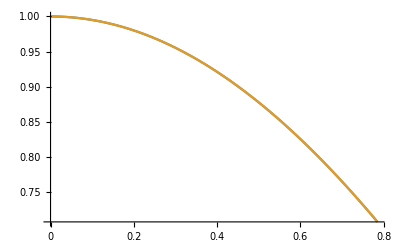

```mathematica
f[x]==Piecewise[{{Cos[x], Cos[x]>=Sin[x]}, {Sin[x], Cos[x]<Sin[x]}}]
Plot[{%[[2]],Cos[x]},{x,0,π/4}]
```

cos(x)와 sin(x)의 크기가 변하는 지점이 바로 x=π/4이기 때문이지요.

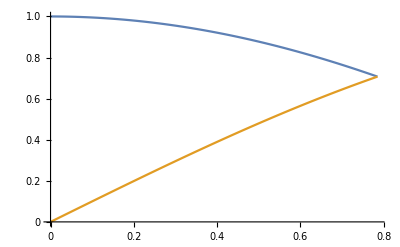

```mathematica
Plot[{Cos[x],Sin[x]},{x,0,π/4}]
```

그럼, 이제 cos(a x)의 그래프를 추가해봅시다.

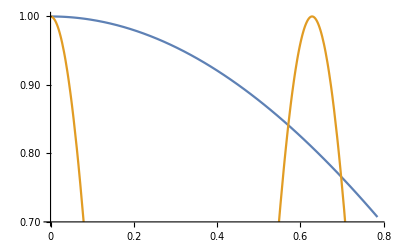

```mathematica
Plot[Evaluate[{Cos[x],Cos[a x]}/.a->10],{x,0,π/4},PlotRange->{0.7,1}]
```

cos(x)와 cos(a x)가 만나는 점을 찾아보면 되겠군요.

```mathematica
Cos[x]==Cos[a x]/.x->π/4
Reduce[%,a]//ExpandAll
```

1/(√2)==Cos[(a π)/4]

C[1]∈ℤ&&(a==-1+8 C[1]||a==1+8 C[1])

이 조건을 만족하는 a를 몇 개 구해봅시다.

```mathematica
a==-1+8 C[1]||a==1+8 C[1]/.Or->List/.C[1]->C//Thread[#,Equal]&//Last
Table[%,{C,-1,5}]//Flatten
```

{-1+8 C,1+8 C}

{-9,-7,-1,1,7,9,15,17,23,25,31,33,39,41}

또한, 닫힌 구간 [0, π/4]에서 세 번 만나려면, 다음 조건을 만족해야 합니다.

```mathematica
a π/4>2π
Reduce[%,a]
```

(a π)/4>2 π

a>8

이 범위를 만족하는 가장 작은 p는 9인 것을 알 수 있죠.

```mathematica
Select[{-9,-7,-1,1,7,9,15,17,23,25,31,33,39,41},#>8&]
```

{9,15,17,23,25,31,33,39,41}

그래프를 그려보면 해당 구간에서 두 그래프가 세 개의 지점에서 만나는 것을 확인할 수 있습니다.

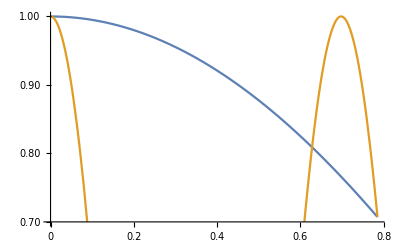

```mathematica
Plot[Evaluate[{Cos[x],Cos[a x]}/.a->9],{x,0,π/4},PlotRange->{0.7,1}]
```

이제 닫힌 구간 [0, 11π/12]에서 두 곡선의 그래프를 그려보면, 8개의 교점을 확인할 수 있다.

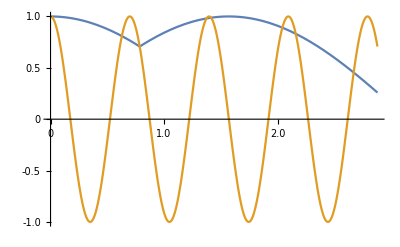

```mathematica
Plot[{Piecewise[{{Cos[x], Cos[x]>=Sin[x]}, {Sin[x], Cos[x]<Sin[x]}}],Cos[9x]},{x,0,11/12 π}]
```

대수적으로 교점을 구해보면,

```mathematica
Piecewise[{{Cos[x], Cos[x]>=Sin[x]}, {Sin[x], Cos[x]<Sin[x]}}]==Cos[9x]
Solve[%&&0<=x<=11/12 π,x]
%//Length
```

(Piecewise[{{Cos[x], Cos[x]≥Sin[x]}, {Sin[x], Cos[x]<Sin[x]}, {0, True}}])==Cos[9 x]

{{x→0},{x→-2 ArcTan[1-√2]},{x→2 ArcTan[√(1/5 (5-2 √5))]},{x→2 ArcTan[Root0.821Root[1+8 #1-28 #1^2-56 #1^3+70 #1^4+56 #1^5-28 #1^6-8 #1^7+#1^8&,6]0.8206787908286604]},{x→2 ArcTan[Root1.87Root[1+8 #1-28 #1^2-56 #1^3+70 #1^4+56 #1^5-28 #1^6-8 #1^7+#1^8&,7]1.8708684117893895]},{x→2 ArcTan[Root0.854Root[1-8 #1-60 #1^2-8 #1^3+134 #1^4+8 #1^5-60 #1^6+8 #1^7+#1^8&,6]0.8540806854634666]},{x→2 ArcTan[Root1.63Root[1-8 #1-60 #1^2-8 #1^3+134 #1^4+8 #1^5-60 #1^6+8 #1^7+#1^8&,7]1.6318516871287896]},{x→2 ArcTan[Root4.17Root[1-8 #1-60 #1^2-8 #1^3+134 #1^4+8 #1^5-60 #1^6+8 #1^7+#1^8&,8]4.165299770090417]}}

8

따라서 q=8이고,

```mathematica
p+q==9+8
```

p+q==17